## Auto routine function

```mathematica
ScaledRHSolver[{scs_,gs_,gms_}]:=Module[{standardf,pts,R,Uls,z0,sc,Cus,uz0,usc,us,gl,lsGs},
standardf=Fun[IdentityMatrix[2]&,Sequence@@##]&/@gms;
pts=standardf//Points;
R=RHSolver[standardf];

Function[x,
Uls={};
Function[ls,
{{z0,sc},lsGs}=ls;
Cus=(Dot@@#)&/@Thread[
Function[uls,
{uz0,usc,us}=uls;
FromValueList[standardf,Cauchy[us,((z0+pts/sc)-uz0)usc]//ToMatrixOfLists//Flatten]//AddIdentityMatrix
]/@Uls
];
gl=Fun[Function[z,#⟦1⟧[x,z0+z/sc]],Sequence@@#⟦2⟧]&/@Thread[{lsGs,gms}];
If[Cus=={},
Uls=Join[{{z0,sc,R[gl]}},Uls],
Uls=Join[{{z0,sc,R[#⟦1⟧.#⟦2⟧.Inverse[#⟦1⟧]&/@Thread[{Cus,gl}]]}},Uls]];
]/@Thread[{scs[x]//Transpose,gs//Transpose}];
(-(DomainIntegrate[#⟦3⟧]⟦1,2⟧)/(2π I #⟦2⟧)&/@Uls)//Total]
]
```

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_,z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_,z_]=GGΣ[y,z]//Inverse;
GG[_][_,_?InfinityQ]:=IdentityMatrix[2];
GG[6][y_,z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[1][y_,z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[3][y_,z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[4][y_,z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[1][y_,z_]=Inverse[Φm[y,z]];
GLC[2][y_,z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[3][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[1][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[2][y_,z_]=S[6].Inverse[Φ[y,z]];
GRC[3][y_,z_]=Inverse[Φm[y,z]];
```

```mathematica
rngg={.5,2.3};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{GGΣ, GGΣin}, {GG[3], GG[6]}, {GG[4], GG[1]}, {GLC[1], GRC[1]}, {GLC[2], GRC[2]}, {GLC[3], GRC[3]}}),({{Line[{.5,3.}], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
```

```mathematica
slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
data=Partition[ReadList[ResearchDirectory<>"/RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]+2 slv[n][Sqrt[-x/2]]
```

```mathematica
data⟦1,1⟧
```

-40.

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

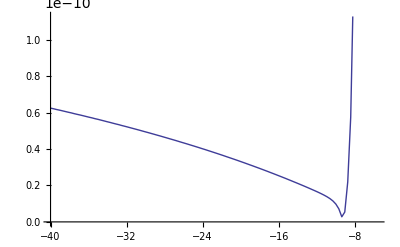

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```